# Caso 2: Modelado de protocolos ARQ para análisis de rendimiento

```mathematica
Clear["Global`*"];
```

```mathematica
<<"/home/david/Documentos/RRT/RandomData.m"
<<"/home/david/Documentos/RRT/drawTx.m"
```

```mathematica
?drawTx`*
```

## Parte 1: simulación de Stop & Wait

Apartado 1
Estudiar librería de representación de paquetes y averiguar el formato del paquete
mu=C/l donde mu es en paq/s, l es bits/paquete y C es bits/segundo
DrawWin: para dibujar una ventana temporal 
DrawPacket: para dibujar los paquetes
SetIniParDraw[prop_time,ack_time]: configura parámetros de transmisión
Paquete = {tiempo_llegada, tasa_servicio*9600, num_sec, error, num_rep} la tasa de servicio 9600 equivale a un segundo (por defecto) y es el tamaño del paquete

Apartado 2
Probar la representación de la librería para un caso particular de Stop & Wait sin errores y con tiempo de propagación 0. Posteriormente hacerlo proporcionando otros valores a cada parámetro

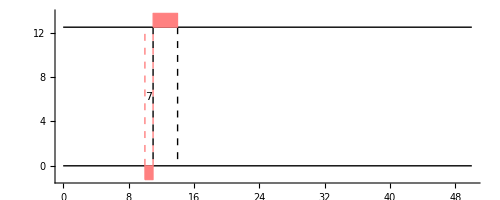

```mathematica
SetIniParDraw[0,3];
GetIniParDraw[];
packet={10,9600,7,0,0};
Show[DrawWin[0,50,10],DrawPacketTx[packet]]
```

```mathematica
(*pktLength+prop_time*2+ack_time=tiempo_llegada --> para que sea Stop&Wait*)
SetIniParDraw[2,2]
pktLength=4;
packets=Table[{n*10,pktLength *9600,n,0,0},{n,0,9}];
Manipulate[Show[DrawWin[0,width,5],Map[DrawPacketTx[#]&,packets]],{width,10,200}]
```

Apartado 3
Cola MM1 (errores incluidos)

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
Map[
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&,
arrivals]]
```

```mathematica
(*Con esto se calcula el tiempo que espera cada paquete en la cola antes de entrar en el enlace (desde que llega hasta que se sirve)*)
InsertionTimeMM1[departures_, service_]:=
Module[{i=0,insertionTime={}},
For[i=0,i<Length[departures],i++,
AppendTo[insertionTime,departures[[i]]-service[[i]]
]
];
Return[insertionTime]
]
```

```mathematica
lambda=10;mu=100;pktNumber=100;p=0.3;
InterArrivalsTime=Table[RandomExp[lambda],pktNumber];
ArrivalsTime=Accumulate[InterArrivalsTime];
ServiceTime=Table[RandomExp[mu],pktNumber];
Departures=FifoSchedulling[ArrivalsTime,ServiceTime];
insertionTimeMM1=InsertionTimeMM1[Departures,ServiceTime];
```

```mathematica
packetsFunc[inserTime_,servTime_,p_ ]:=
Module[{i,packets={}},
For[i=1,i<Length[inserTime],i++,
If[RandomReal[]<p,
AppendTo[packets,{inserTime[[i]],servTime[[i]]*9600,i-1,1,0}],
AppendTo[packets,{inserTime[[i]],servTime[[i]]*9600,i-1,0,0}]
]
];
Return[packets]
]
```

```mathematica
packetsMM1=packetsFunc[insertionTimeMM1,ServiceTime,p];
```

```mathematica
propTime=0.05;ackTime=0.004;
SetIniParDraw[propTime,ackTime];
```

```mathematica
Manipulate[Show[DrawWin[0,width,10],Map[DrawPacketTx[#]&,packetsMM1]],{width,0,1}]
```

```mathematica
insertionTimeMM1[[1;;10]]
```

{0,0.0257433,0.0400615,0.135858,0.392525,0.528921,0.572719,0.612568,0.759577,0.781621}

```mathematica
packetsMM1[[1;;5]]
```

{{0,3.91279,0,1,0},{0.0257433,62.4021,1,0,0},{0.0400615,55.8302,2,0,0},{0.135858,134.147,3,1,0},{0.392525,55.3966,4,0,0}}

### Protocolo Stop&Wait (sin errores)

```mathematica
InsertionTimeSW[arrivTime_, servTime_,propTime_,ackTime_]:=
Module[{inserTime={arrivTime[[1]]},i,check},
For[i=2,i<Length[arrivTime],i++,
check=inserTime[[i-1]]+servTime[[i-1]]+2*propTime+ackTime;If[arrivTime[[i]]≤  check,AppendTo[inserTime,check],AppendTo[inserTime,arrivTime[[i]]]
]
];
Return[inserTime]
]
```

```mathematica
insertionTimeSW=InsertionTimeSW[ArrivalsTime,ServiceTime,propTime,ackTime];
```

```mathematica
insertionTimeSW[[1;;5]]
```

{0.0257433,0.130151,0.240651,0.392525,0.528921}

```mathematica
p=0;
packetsSW=packetsFunc[insertionTimeSW,ServiceTime,p];
```

```mathematica
Manipulate[Show[DrawWin[0,width,3],Map[DrawPacketTx[#]&,packetsSW]],{width,0,10}]
```

### Protocolo Stop&Wait (con errores)

## Parte 2: comparar rendimientos teóricos de Stop & Wait con simulaciones

```mathematica
(*Aqui hay que hacer comparaciones de los valores teoricos con los obtenidos de la simulación anterior, cuando se introducen errores en los paquetes*)
```

## Parte 3: simulación de Go-Back-N

### Protocolo GoBackN (sin errores)

```mathematica
(*InsertionTimeGBN[arrivTime_,servTime_,deparTime_,propTime_,ackTime_,mod_]:=
Module[{inserTime={arrivTime[[1]]},i,inserted=1},
For[i=2,i<Length[arrivTime],i++,
If[inserted==mod,
AppendTo[inserTime,deparTime[[i-1]]+2*propTime+ackTime];inserted=0,
AppendTo[inserTime,deparTime[[i-1]]];inserted++
]
];
Return[inserTime]
]*)
```

```mathematica
(*A esta funcion le falta que tenga en cuenta cuando un paquete llega mas tarde del departure del anterior (tener en cuenta los momentos de cola vacia), y que la ventana sea deslizante (ahora mismo es fija)*)
InsertionTimeGBN[arrivTime_,servTime_,deparTime_,propTime_,ackTime_,mod_]:=
Module[{inserTime={arrivTime[[1]]},i,inserted=1},
For[i=2,i<Length[arrivTime],i++,
If[inserted==mod,
AppendTo[inserTime,inserTime[[i-1]]+servTime[[i-1]]+2*propTime+ackTime];inserted=1,
AppendTo[inserTime,inserTime[[i-1]]+servTime[[i-1]]];inserted++
]
];
Return[inserTime]
]
```

```mathematica
mod=4;
```

```mathematica
insertionTimeGBN=InsertionTimeGBN[ArrivalsTime,ServiceTime,Departures,propTime,ackTime,mod];
```

```mathematica
insertionTimeGBN[[1;;5]]
```

{0.0257433,0.0261509,0.0326511,0.0384668,0.15644}

```mathematica
p=0;
packetsGBN=packetsFunc[insertionTimeGBN,ServiceTime,p];
```

```mathematica
Manipulate[Show[DrawWin[0,width,mod],Map[DrawPacketTx[#]&,packetsGBN]],{width,0,1}]
```

### Protocolo GoBackN (con errores)

## Parte 4: comparar rendimientos teóricos de Go-Back-N con simulaciones

```mathematica
(*Aqui hay que hacer comparaciones de los valores teoricos con los obtenidos de la simulación anterior, cuando se introducen errores en los paquetes*)
```